# Splitting mixed cell groups

The heavily contaminated assemblies (> 20% contamination) correspond to cell groups containing cells of multiple species. These are the false positive cases in the clustering. To split the contaminated cell groups, an abundance-based approach is applied. We extract the contigs with lengths > 1k in the assemblies, and use the average sequencing depths (i.e. abundances) of the contigs as a feature to cluster the cells potentially from the same species.

Assume that the co-assembly of the cell group g, which consists of n cells, has m contigs with lengths > 1k. Let d_ijdenote the average sequencing depth of contig j in cell i. Then for each cell i in group g, d_i=(d_(i 1), d_(i 2),…, d_im)ᵀ is a column vector describing the contig abundances into the cell’s sequencing.

Each of the mixed cell groups, has a matrix describing the abundances across contigs in cells.

D=(d_1 d_2 ⋯ d_n)=(d_ij)_(m×n)

The normalization to get the feature vectors is a combination of both the row normalization and the column normalization. The row normalization reduces the impact of contigs’ contribution disparity to different cells. And the column normalization reduces the bias in the dissimilarity estimation of the cells, i.e. distances of the cells’ contig abundance vectors. The normalization and distance computation are with respect to the 2-norm.

Below is to validate the choice of 1.4 as the cut-off value for splitting the dendrogram.

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
<<HierarchicalClustering`
```

You may chose other bin by modifying the “binName” variable. Check out the available bins in the “data/splitting-vectors” directory. The results show no much difference for different input.

```mathematica
binName="11";
vectors=#⟦1⟧->#⟦2;;⟧&/@Import["data/splitting-vectors/"<>binName<>".tsv.gz"];
dendro=Agglomerate[Reverse/@vectors,Linkage->"Complete"];
```

Agglomerate::ties: 9 ties have been detected; reordering input may produce a different result.

Change the number of clusters “nClusters” to split the dendrogram, until you see a strong pattern of separated sub-matrices on the diagonal.

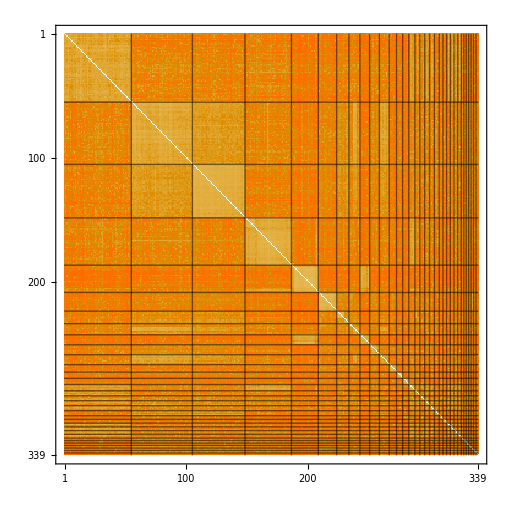

```mathematica
nClusters=34;
clusters=SortBy[ClusterSplit[dendro,nClusters]/.c_Cluster:>ClusterFlatten[c],Minus@*Length];
lines=Graphics[{RGBColor[0,0,0,0.5],
Line[{{
{0,(Length[Flatten[clusters]]-#)},
{Length[Flatten[clusters]],Length[Flatten[clusters]]-#}},{
{#,0},
{#,Length[Flatten[clusters]]}
}}]}]&/@Accumulate[Select[Length/@clusters,#≥2&]];
Show[MatrixPlot[System`DistanceMatrix[Flatten[clusters]/.vectors]],lines]
```

Flatten the matrix leaving out the diagonal,

```mathematica
FlattenWithoutDiagonal[submat_List]:=Module[{n},
n=Length[submat];
Flatten[Table[Delete[submat⟦i⟧,i],{i,n}]]
];
```

The distance matrices of the clusters,

```mathematica
distMats=System`DistanceMatrix/@(clusters/.vectors);
```

Histogram for the distances within the first cluster. You may modify the number in the double bracket to see the others.

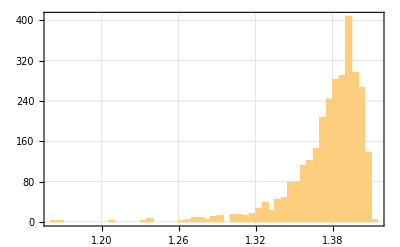

```mathematica
Histogram[FlattenWithoutDiagonal[distMats⟦1⟧],PlotRange->Full,PlotTheme->"Detailed"]
```

Histogram for the distances between different cluster. You can also modify the value within the double bracket.

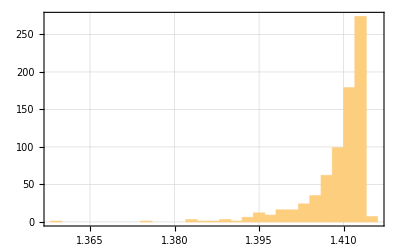

```mathematica
diffMat=System`DistanceMatrix@@((clusters/.vectors)⟦{2,6}⟧);
Histogram[Flatten@diffMat,PlotRange->Full,PlotTheme->"Detailed"]
```

This is a justification for choosing 1.4 as a hard cut-off in hierarchical clustering for splitting the mixed cell groups.